```mathematica
chi60=(x-22)(x-2)^42(x+6)^15(x+8)^2;
adj5C4=({{0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0}});
```

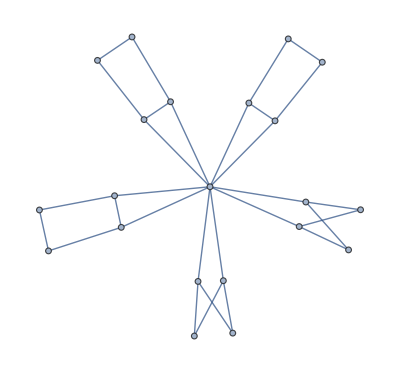
```mathematica
theonlyvalid21=-Graphics-;
adj21=AdjacencyMatrix[theonlyvalid21];
```

```mathematica
P=(x+4)IdentityMatrix[20]+adj5C4+(10(x+6))/((x+8)(x-22))ConstantArray[1,{20,20}];
Pinv=Inverse[P]//Factor;
```

```mathematica
Det[P]//Factor
```

((-12+x) (-2+x) (2+x)^5 (4+x)^10 (6+x)^5)/((-22+x) (8+x))

```mathematica
Pinvx11=Pinv/.x->11;
```

```mathematica
((-12+x) (-2+x)^21 (2+x)^5 (4+x)^10 (8+x))/(6+x)^2
```

```mathematica
((-12+x) (-2+x)^21 (2+x)^5 (4+x)^10 (8+x))/(6+x)^2/.x->11
```

-445118506640977978265903540963349609375/289

```mathematica
compgraph454=ConstantArray[0,{454,454}];
For[i=2,i≤454,i++,
If[Mod[i,15]==0,Print[i]];
For[j=1,j≤i-1,j++,
n=23;
mat=ConstantArray[0,{n,n}];
mat[[Range[21],Range[21]]]=adj21;
mat[[n-1,Range[20]]]=all454[[i]];
mat[[Range[20],n-1]]=all454[[i]];
mat[[n,Range[20]]]=all454[[j]];
mat[[Range[20],n]]=all454[[j]];

S=(11+4)IdentityMatrix[n-20]+(10(11+6))/((11+8)(11-22))ConstantArray[1,{n-20,n-20}];

Q=mat[[Range[20],Range[21,n]]];
Q=Q+(9 11+82)/((11+8)(11-22))ConstantArray[1,{20,n-20}];

detx11=Det[S-Transpose[Q].Pinvx11.Q]*(-445118506640977978265903540963349609375/289);
If[IntegerQ[detx11],compgraph454[[i,j]]=1;compgraph454[[j,i]]=1];
]
]//AbsoluteTiming
```

15

30

45

60

75

90

105

120

135

150

165

180

195

210

225

240

255

270

285

300

315

330

345

360

375

390

405

420

435

450

{330.892,Null}

```mathematica
AdjacencyGraph[compgraph454]//FindClique
```

{{1,10,15,16,31,35,44}}